## Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

### Defenitions

```mathematica
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
(*M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};*)
```

#### Tests:

```mathematica
M.{0,Sqrt[Qp],0,Sqrt[Qm],0,0}//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&
```

{0,0,0,0,0,0}

```mathematica
M//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&//MatrixForm
```

(√(Qm/Qp) (√(1-a^2) γa+a γp) | √(Qm/Qp) (a γa-√(1-a^2) γp) | -√(1-a^2) γa-a γp | -a γa+√(1-a^2) γp | √Qp κ | √Qp κ
√(Qm/Qp) (-a γa+√(1-a^2) γp) | √(Qm/Qp) (√(1-a^2) γa+a γp) | a γa-√(1-a^2) γp | -√(1-a^2) γa-a γp | √Qp α κ | √Qp α κ
-√(1-a^2) γa+a γp | a γa+√(1-a^2) γp | √(Qp/Qm) (√(1-a^2) γa-a γp) | -√(Qp/Qm) (a γa+√(1-a^2) γp) | √Qm κ | -√Qm κ
-a γa-√(1-a^2) γp | -√(1-a^2) γa+a γp | √(Qp/Qm) (a γa+√(1-a^2) γp) | √(Qp/Qm) (√(1-a^2) γa-a γp) | √Qm α κ | -√Qm α κ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

### For gradient method

```mathematica
avars={a5,a4,a3,a2,a1};
vars={Qp,Qm,ψ};
params={Λ,γp};
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
```

Part::take: Cannot take positions 4 through 5 in {Qp,Qm,ψ}.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

### Solution

```mathematica
(*Solving stationary problem*)
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}]
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];


(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p=-CoefficientList[CharacteristicPolynomial[(tmp2/.Nsol),λ],λ];
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
If[AllTrue[p,Positive],
If[AllTrue[Dets,Positive],
Print["System is stable"];
Print[p//MatrixForm];
Print[Dets//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[Dets//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm]
]
```

{Qp→0.350028,Qm→0.350028,a→-1.08553×10^-16}

Some Hurwitz determinants are negative:

(1.91066×10^7
422612.
68199.
1328.33
52.4401
1)

(1458.73
-4.31373×10^12)

```mathematica
p
```

{1.91066×10^7,422612.,68199.,1328.33,52.4401,1}

```mathematica
({{3.232764872790355*^-8}, {1.910655999879378*^7}, {422611.74144311715}, {68199.01081752068}, {1328.32937396901}, {52.44011333711123}, {1}})({{52.44011333711123}, {1458.7321024281991}, {-6.073344503642392*^7}, {-4.313731141096*^12}, {-8.24205628660157*^19}}){Qp->0.3500283342778091,Qm->0.35002833427780905,a->-1.0848001355988288*^-16}
```

### Plotting by pixels v0

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
ysub={Sqrt[1-a^2]-> -Sqrt[1-a^2]};
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];

Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0.5;
]
(*result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] ***=> D4 fails****)
,
result[[i,j]]=0;
];
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.Nsol//Chop)==  0]],result[[i,j]]=-1,]
]
];
Image[Reverse[result]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.107997,0.906551,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.123634,0.910422,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {Qp,Qm,a} = {0.139076,0.914214,1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

-Graphics-

```mathematica
Select[result,#==-1 &]
```

{}

```mathematica
newres=Table[If[result[[i,j]]>0.5,1,0],{i,1,Nμ},{j,1,Nγp}];
contour=Abs[newres[[2;;,2;;]]-newres[[;;-2,2;;]]]+Abs[newres[[2;;,2;;]]-newres[[2;;,;;-2]]];
rgb=ConstantArray[0,{Nμ,Nγp,3}];
rgb[[;;,;;,2]]=newres;
rgb[[2;;,2;;,1]]=contour;
Image[Reverse[rgb]]
```

-Graphics-

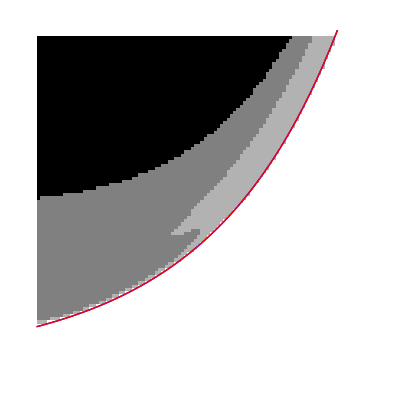

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuMine[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
Diff[γp_]:=(MuMine[γp]-Mu[γp])/MuMine[γp];

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
lmp=Plot[(MuMine[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick}];
Show[ap,lmp,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

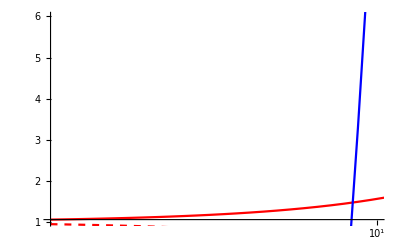

```mathematica
pl1 = Plot[1+γd*x/(γ (α κ - x)),{x,1,100},PlotStyle->Red,ScalingFunctions-> {"Log10",None}];
pl2 =Plot[1-γd/γ+2α x/γ,{x,1,100},PlotStyle->Blue,ScalingFunctions-> {"Log10",None}];
pl3 = Plot[1-γd*x/(γ (α κ + x)),{x,1,100},PlotStyle->{Red,Dashed},ScalingFunctions-> {"Log10",None}];
pl4 =Plot[1-γd/γ-2α x/γ,{x,1,100},PlotStyle->{Blue,Dashed},ScalingFunctions-> {"Log10",None}];
Show[pl1,pl2,pl3,pl4,PlotRange->{{0,1},{1,6}}]
```

```mathematica
oldresult=result;
```

### Plotting bound

```mathematica
CheckStability[κ_,α_,γ_,γd_,γp_,γa_,μ_,Qp0_,Qm0_,a0_]:=Module[{Eq1,Eq2,Eq3,M,Dets,Nsol},

Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};

Nsol=FindRoot[({Eq1,Eq2,Eq3}/.{μ-> μ})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

	If[AllTrue[Dets,Positive],
{1,Nsol},
{0,Nsol}],
{0,Nsol}
]
];
```

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

(*Initial grid test*)
Nμ=100;
Nγp=100;
μmin=1.;
μmax=4.;
γpmin=10.;
γpmax=100.;
accuracy=1.*^-5;

μs=CoordinateBoundsArray[{{μmin,μmax}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{Log10[γpmin],Log10[γpmax]}},Into[Nγp]]//Flatten//Power[10,#]&;

result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
res=CheckStability[κ,α,γ,γd,γps[[j]],γa,μs[[i]],Qp0,Qm0,a0];
result[[i,j]]=res[[1]];
Qp0=Qp/.res[[2]];Qm0=Qm/.res[[2]];a0=a/.res[[2]];
]];
contour=Abs[result[[2;;,2;;]]-result[[;;-2,2;;]]]+Abs[result[[2;;,2;;]]-result[[2;;,;;-2]]];
```

```mathematica
CheckStability[κ,α,γ,γd,γps[[50]],γa,μs[[2]]]
```

1

```mathematica
CheckStability[κ_,α_,γ_,γd_,γp_,γa_,μ_]:=Module[{Qp0,Qm0,a0,Nsol},
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

	If[AllTrue[Dets,Positive],
1,
0],
0
]
];
```

1

```mathematica
Image[Reverse[result]]
```

-Graphics-

```mathematica
cnt=Thinning[contour];
(*find initial pixel*)
pt={0,0};
notfind=True;
For[i=1,i<Nμ,i++,
If[cnt[[i,1]]==1,pt={i,1};notfind=False;Break,]
];
If[notfind,(*TODO search fo other bound*),];
(*creating initial line*)
used=ConstantArray[0,Dimensions[cnt]];
used[[pt[[1]],pt[[2]]]]=1;
points={pt};
nomore=False;
While[Not[nomore],
pt=Nearest[DeleteCases[DeleteCases[Flatten[Table[{pt[[1]]+i,pt[[2]]+j},{i,-1,1},{j,-1,1}],1],x_/;x[[1]]<1||x[[1]]≥ Nμ||x[[2]]<1||x[[2]]≥ Nγp],x_/;cnt[[x[[1]],x[[2]]]]==0],pt,
DistanceFunction->((used[[First[#2],Last[#2]]])&)][[1]];
If[used[[pt[[1]],pt[[2]]]]==1,nomore=True;Print[pt],used[[pt[[1]],pt[[2]]]]=1;points=Append[points,pt]];
]
```

{98,59}

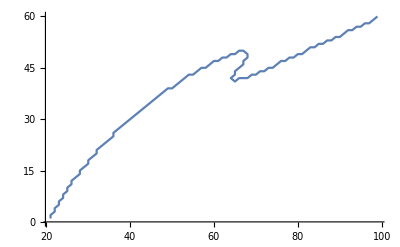

```mathematica
(*Search with bisection method until given precision*)
For[i=2,i< Length[points],i++,
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]+1);
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]+1)/Nγp);
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]+1);
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]+1)/Nγp);
res=result[[pt[[1]]+1,pt[[2]]+1]];
res1=
]
```

```mathematica
i=2;
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
μ=μmin+(μmax-μmin)/Nμ*pt1[[1]]
γp=γpmin*(γpmax/γpmin)^(pt1[[2]]/Nγp)
```

1.65683

10.364

```mathematica
{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N
```

{0.894427,-0.447214}

```mathematica
{μs[[pt[[1]]+1]],γps[[pt[[2]]+1]]}
{μs[[pt[[1]]+2]],γps[[pt[[2]]+2]]}
```

{1.63,10.4713}

{1.66,10.7152}

```mathematica
Image[Reverse[cnt]]
```

-Graphics-

```mathematica
f=ListInterpolation[points,InterpolationOrder->2];

Plot[f[x],{x,0,4}]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,1}.

-Graphics-

```mathematica
Clear[X,Y,p2,L];
X={xm1,0,xp1};
Y={ym1,0,yp1};
L[j_,x_]:=Product[If[i==j,1,(x−X[[i]])/(X[[j]]−X[[i]])],{i,1,3}];
p2[x_]:=Sum[Y[[i]]*L[i,x],{i,1,3}]
```

```mathematica
D[p2[x],x]/.{x-> 0}//FullSimplify
```

(-xp1^2 ym1+xm1^2 yp1)/(xm1 (xm1-xp1) xp1)

```mathematica
p2[x]
```

(x (x-xp1) ym1)/(xm1 (xm1-xp1))+(x (x-xm1) yp1)/(xp1 (-xm1+xp1))

### Plotting by pixels v2

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];

p=-CoefficientList[CharacteristicPolynomial[(tmp3/.{Λ-> μ}/.Nsol),λ],λ];

If[AllTrue[p,Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)

If[AllTrue[Dets,Positive],
result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] 
,
result[[i,j]]=0
],
If[oldresult[[i,j]]>0,Print[i," ",j],]
]
]];
Image[Reverse[result]]
```

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

General::stop: Further output of CharacteristicPolynomial::inf will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.107997,0.906551,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.123634,0.910422,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.139076,0.914214,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

-Graphics-

```mathematica
Image[Reverse[oldresult-result]]
Image[Reverse[oldresult]]
```

-Graphics-

-Graphics-

```mathematica
μ=μs[[100]];
γp=γps[[83]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
```

```mathematica
p
```

{1.02348×10^10,1.18555×10^8,-1.30236×10^6,35269.8,121.689}